# NarvAC v2

### Autor: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

## Auxiliary

```mathematica
HalfSplit[l_]:=TakeDrop[l, Floor[Length[l]/2]];

Unprotect[BitAnd];
BitAnd[1,x_]:=x;
BitAnd[x_,1]:=x;
Protect[BitAnd];

Unprotect[BitNot];
BitNot[0] := 1;
BitNot[1] := 0;
Protect[BitAnd];

DecimalToBinary[n_,size_ :8]:=PadLeft[IntegerDigits[n,2],size];
BinaryToDecimal[l_]:=FromDigits[l,2];
```

## Visualization

### Circuit result tables

Tables of input-output for simple circuits.

```mathematica
VisualizeGate[module_] := Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,{Apply[module,#]}]&,Tuples[{0,1},2]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],2],{"Result"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];
VisualizeAdder[module_,inputSize_,flagName_] := Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,Apply[module,#]]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{flagName,"Result"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];

VisualizeMultiplexer[mux_,inputSize_]:=Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,{mux[#,Take[Alphabet[],2^inputSize]]}]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{"Selection"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];
```

```mathematica
VisualizeGate[BitAnd]
```

A | B | Result
0 | 0 | 0
0 | 1 | 0
1 | 0 | 0
1 | 1 | 1

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

```mathematica
VisualizeMultiplexer[Mux4to1,2]
```

A | B | Selection
0 | 0 | a
0 | 1 | b
1 | 0 | c
1 | 1 | d

### Tree structure of expression

There are two ways to represent an expression as a graph. First by drawing the expression as a tree form, for example:

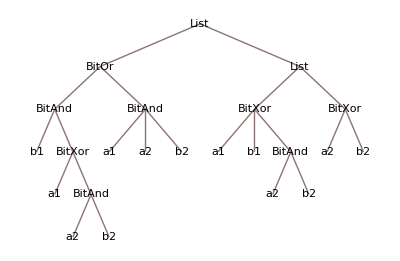

```mathematica
TreeForm[ALUAdder[{a1,a2},{b1,b2}]]
```

or by transforming the tree in a more compact form by removing the redundancy of repeated variables, for example:

```mathematica
CompactTreeForm[ALUAdder[{a1,a2},{b1,b2}]]
```

The simple TreeForm has the disadvantage of quickly being unpractical with complex expressions. The function
PlotExpression[expr, opts] offers a more visible representation of a TreeForm for large expressions and
PlotInteractiveSystem[system] plots an interactive TreeForm representation of the circuit.
Analogously,
CompactTreeForm[system] plots an expression as a graph and
PlotCompactInteractiveSystem[system] plots an interactive graph of the circuit.

#### Evaluation of expression heads

```mathematica
EvaluateHead[expr_,values_]:=ReplaceRepeated[expr,{f_Symbol[arg__]:>ReplaceAll[f[arg],values][arg]}];
NestedEvaluate[expr_,values_]:=If[Head[expr]===List,
Map[NestedEvaluate[#,values]&,Level[expr,1]],
ReplaceAll[EvaluateHead[expr,values],values]
];
```

#### Examples

```mathematica
expr = ALUAdder[{a1,a2},{b1,b2}]
```

{BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]],{BitXor[a1,b1,BitAnd[a2,b2]],BitXor[a2,b2]}}

```mathematica
NestedEvaluate[expr,{a1->0,a2->1,b1->0,b2->1}]
```

{0[0[0,1[0,1[1,1]]],0[0,1,1]],{1[0,0,1[1,1]],0[1,1]}}

#### Compact tree graph

```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];
TreeFormToGraph[treeForm_]:=Module[
{graph,tree=ToExpression@ToBoxes@treeForm,order,pos,label},
label=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity];
{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
graph = Graph[DirectedEdge@@@order,VertexLabels->label,VertexCoordinates->MapIndexed[Rule[First[#2],#]&,pos]];
{graph,ReleaseHold[label]}
];

RuleListToMatrix[list_]:=Transpose[{list[[All,1]],list[[All,2]]}];
SeparateFirst[l_]:={First[l],Drop[l,1]};
MakeReplaceRules[fixed_,toBeReplaced_]:=Map[(vertex_->#):>(vertex->fixed)&,toBeReplaced];

ReplaceRuleForLabel[labels_,labelName_]:=Block[{fixed,toBeReplaced,replaceRules},
{fixed,toBeReplaced}=SeparateFirst[Cases[RuleListToMatrix[labels],{vertex_,labelName}:>vertex]];
replaceRules = MakeReplaceRules[fixed,toBeReplaced];
MakeReplaceRules[fixed,toBeReplaced]
];
ReplaceRuleForAllLabels[labels_]:=Block[{nameLabels},
nameLabels = DeleteCases[
DeleteDuplicates[labels[[All,2]]],
x_ /;MemberQ[{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association},x]
];
Flatten[Map[ReplaceRuleForLabel[labels,#]&,nameLabels]]
];

CompactTreeForm[expr_,opts: OptionsPattern[]]:=Block[{graph,labels,newGraph,deleteVertex,newLabels},
{graph,labels} = TreeFormToGraph[TreeForm[expr]];
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]];
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]];
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]];

Graph[
ReplaceAll[newGraph,x_->y_:>y->x],
VertexLabels->newLabels,
DirectedEdges->True,
FilterRules[{opts},Options[Graph]]
]
];
```

```mathematica
DecorateVertexes[labels_]:=Block[{and,xor,or,not,list},
and = Map[Style[#,RGBColor[0.03, 0.8200000000000001, 0.]]&,Cases[labels,HoldPattern[x_->BitAnd]:>x]];
xor = Map[Style[#,RGBColor[0.9, 0.14, 0.]]&,Cases[labels,HoldPattern[x_->BitXor]:>x]];
or = Map[Style[#,RGBColor[0.26, 0.39, 1.]]&,Cases[labels,HoldPattern[x_->BitOr]:>x]];
not = Map[Style[#,RGBColor[1., 1., 0.04]]&,Cases[labels,HoldPattern[x_->BitNot]:>x]];
list = Map[Style[#,RGBColor[0.12, 0.1, 0.]]&,Cases[labels,HoldPattern[x_->List]:>x]];

Join[and,xor,or,not,list]
];

Options[CompactEvaluatedTreeForm]=Union[{"ShowLabels"->Automatic},Options[Graph],Options[HighlightGraph]];
CompactEvaluatedTreeForm[expr_,values_,opts: OptionsPattern[]]:=Block[
{
graph,labels,newGraph,deleteVertex,newLabels,
evaluatedGraph,evaluatedLabels,newEvaluatedGraph,deleteEvaluatedVertex,newEvaluatedLabels,
highlightedVertexes,highlightedEdges
},
{graph,labels} = TreeFormToGraph[TreeForm[expr]];
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]];
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]];
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]];

{evaluatedGraph,evaluatedLabels} = TreeFormToGraph[TreeForm[NestedEvaluate[expr,values]]];
newEvaluatedGraph = ReplaceAll[EdgeList[evaluatedGraph],ReplaceRuleForAllLabels[evaluatedLabels]];
deleteEvaluatedVertex = Complement[evaluatedLabels[[All,1]],VertexList[newEvaluatedGraph]];
newEvaluatedLabels = DeleteCases[evaluatedLabels,x_/;MemberQ[deleteEvaluatedVertex,First[x]]];

highlightedVertexes = Cases[newEvaluatedLabels,HoldPattern[x_->1]:>x];
highlightedEdges = Select[EdgeList[newGraph],MemberQ[highlightedVertexes,Last[#]]&];

graph = Graph[
ReplaceAll[newGraph,x_->y_:>y->x],
If[OptionValue["ShowLabels"]===Automatic,
VertexLabels->newLabels,
VertexLabels->None
],
DirectedEdges->True,
ImageSize->500,
FilterRules[{opts},Options[Graph]]
];
GraphPlot[
HighlightGraph[
graph,
Join[ReplaceAll[highlightedEdges,x_->y_:>y->x],DecorateVertexes[labels]],
VertexSize->0.2,
FilterRules[{opts},Options[HighlightGraph]]
]
]
];

BinaryResultToDecimal[n_List /; Depth[n]>2]:=Map[BinaryResultToDecimal,n];
BinaryResultToDecimal[n_List /; Depth[n]==2]:=FromDigits[n,2];
BinaryResultToDecimal[n_]:=n;

GetSymbols[system_]:=Complement[
DeleteDuplicates[Level[system,{-1},Heads->True]],
{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association}
];
PlotCompactInteractiveSystem[system_,opts: OptionsPattern[]]:=DynamicModule[{symbols,controllerSymbols,boxes,controls,gathered},
symbols = GetSymbols[system];
controllerSymbols = Map[Symbol[StringJoin[SymbolName[#],ToString[$ModuleNumber]]]&,symbols];
boxes = Map[Checkbox[Dynamic[#],{0,1}]&,controllerSymbols];
controls = Panel[Multicolumn[Map[Row[{SymbolName[#[[1]]]<>": ",#[[2]]}]&,Transpose[{symbols,boxes}]],5],Style["Input",Bold]];
gathered = GatherBy[symbols,StringTake[SymbolName[#],1]&];

Panel[
Column[
{
controls,
Framed[Row[{Style["Input in decimal: ",Bold],Dynamic[BinaryResultToDecimal[ReplaceAll[gathered,Thread[symbols->controllerSymbols]]]]}]],
Framed[Row[{Style["Result: ",Bold],Dynamic[ReplaceAll[system,Thread[symbols->controllerSymbols]]]}]],
Framed[Row[{Style["Result in decimal: ",Bold],Dynamic[BinaryResultToDecimal[ReplaceAll[system,Thread[symbols->controllerSymbols]]]]}]],
Framed[Dynamic[CompactEvaluatedTreeForm[system,Thread[symbols->controllerSymbols],opts]]]
}
]
]
,
SaveDefinitions->True
];
```

```mathematica
PlotCompactInteractiveSystem[Mux2to1[{s},{i1,i2}]]
```

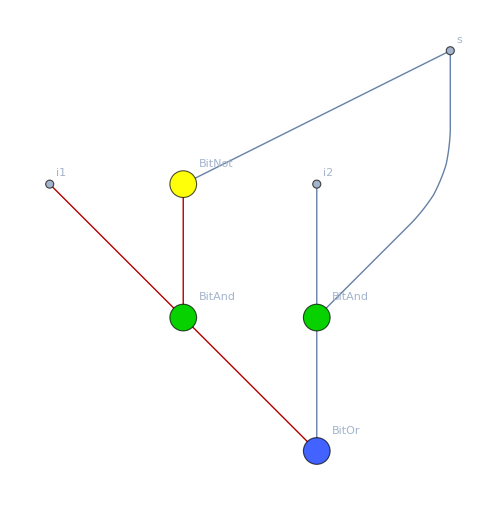

```mathematica
CompactEvaluatedTreeForm[Mux2to1[{s},{i1,i2}],{s->0,i1->1,i2->0}]
```

## Multiplexer

The multiplexer is a device that selects between input signals  {i_0, i_1,... , i_n} and forwards it to a single output line by selecting it with a signal {s_(1,)..., s_m} with m = 2^n.
In the context of this computer, multiplexers are used to select output signals of a circuit, for example, selecting the desired output of the ALU by using an opcode.

-Graphics-

Figure: Schematic of a 2-to-1 Multiplexer. It can be equated to a controlled switch.
Source: https://en.wikipedia.org/wiki/Multiplexer

### 2 to 1

Selects a two input signal  {i_0, i_1} by the 1 bit selector signal {s_1}

-Graphics-

```mathematica
Mux2to1[{select_},{input1_,input2_}]:=BitOr[BitAnd[input1,BitNot[select]],BitAnd[input2,select]];
```

### 4 to 1

Selects a four input signal  {i_0, i_1, i_2, i_3} by a two bit selector {s_0, s_1}.

-Graphics-

```mathematica
Mux4to1[{select1_,select2_},{input1_,input2_,input3_,input4_}]:=Mux2to1[
{select1},
{
Mux2to1[{select2},{input1,input2}],
Mux2to1[{select2},{input3,input4}]
}
];
```

### 8 to 1

Selects a eight input signal  {i_0, i_1, i_2, i_3,i_4, i_5, i_6, i_7}  by a four bit selector {s_0, s_1,s_2, s_3}. It is possible to build a 8:1 multiplexer using two 4:1 multiplexers.

-Graphics-

```mathematica
Mux8to1[{select1_,select2_,select3_},{input1_,input2_,input3_,input4_,input5_,input6_,input7_,input8_}]:=
Mux2to1[
{select1},
{
Mux4to1[{select2,select3},{input1,input2,input3,input4}],
Mux4to1[{select2,select3},{input5,input6,input7,input8}]
}
];
```

### Arbitrary size multiplexer

For an arbitrary sized multiplexer a recursive implementation is used.

```mathematica
MultiplexerNTo1[2,{select_},input__]:=BitOr[BitAnd[First[input],BitNot[select]],BitAnd[Last[input],select]];
MultiplexerNTo1[n_,select_,input__]:=Block[{partInput},
partInput = HalfSplit[input];
MultiplexerNTo1[
2,
{First[select]},
{
MultiplexerNTo1[n/2,Rest[select],First[partInput]],
MultiplexerNTo1[n/2,Rest[select],Last[partInput]]
}
]
];
MultiplexerNToM[n_,m_,select_,input__]:=Table[MultiplexerNTo1[n,select,input[[All,i]]],{i,m}];
```

#### Example

```mathematica
VisualizeMultiplexer[MultiplexerNTo1[16,#1,#2]&,4]
```

A | B | C | D | Selection
0 | 0 | 0 | 0 | a
0 | 0 | 0 | 1 | b
0 | 0 | 1 | 0 | c
0 | 0 | 1 | 1 | d
0 | 1 | 0 | 0 | e
0 | 1 | 0 | 1 | f
0 | 1 | 1 | 0 | g
0 | 1 | 1 | 1 | h
1 | 0 | 0 | 0 | i
1 | 0 | 0 | 1 | j
1 | 0 | 1 | 0 | k
1 | 0 | 1 | 1 | l
1 | 1 | 0 | 0 | m
1 | 1 | 0 | 1 | n
1 | 1 | 1 | 0 | o
1 | 1 | 1 | 1 | p

#### Visualization

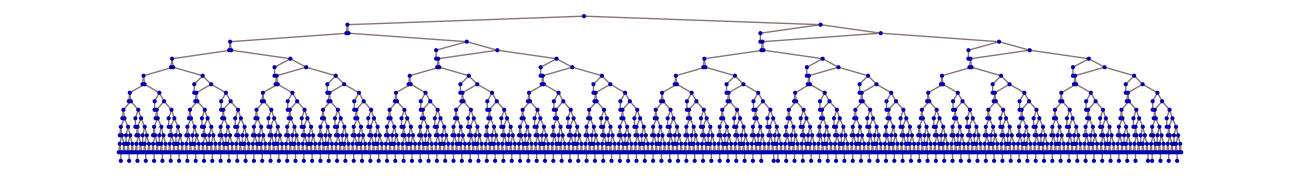

```mathematica
selectSymbols = Table[Symbol["s"<>ToString[i]],{i,1,8}];
inputSymbols = Table[Symbol["i"<>ToString[i]],{i,1,256}];
TreeForm[MultiplexerNTo1[256,selectSymbols,inputSymbols],VertexLabeling->Automatic,ImageSize->1300]
```

### Multiplexer selection by opcode

Auxiliary function to pair input-output pairs in a multiplexer by using opcodes.

```mathematica
MuxInputByOpcode1Bit[n_,opcodeAndOutput_]:=Block[{addresses,missing},
addresses = Tuples[{0,1},n]; (* Generate the list of all opcode inputs.  *)
missing = Thread[{Complement[addresses,opcodeAndOutput[[All,1]]],0}]; (* Select the ones with no inputs and map them to zero. *)
Return[SortBy[Join[missing,opcodeAndOutput],First][[All,2]]] (* Join missing opcodes with the given opcodes and sort. *)
];
MuxInputByOpcodeMBit[n_,m_,opcodeAndOutput_]:=Block[{addresses,zero,missing},
addresses = Tuples[{0,1},n]; (* Generate the list of all opcode inputs.  *)
zero = ConstantArray[0,m];
missing = Table[{i,zero},{i,Complement[addresses,opcodeAndOutput[[All,1]]]}]; (* Select the ones with no inputs and map them to zero. *)
Return[SortBy[Join[missing,opcodeAndOutput],First][[All,2]]] (* Join missing opcodes with the given opcodes and sort. *)
];

Mux8ToM[m_,select_,input__]:=Table[Mux8to1[select,input[[All,i]]],{i,m}];
Multiplexer3BitTo1Bit[opcode_,opcodeAndOutput_]:=Mux8to1[opcode,MuxInputByOpcode1Bit[3,opcodeAndOutput]];
Multiplexer3BitToMBit[m_,opcode_,opcodeAndOutput_]:=Mux8ToM[m,opcode,MuxInputByOpcodeMBit[3,m,opcodeAndOutput]];
```

#### Example

```mathematica
MuxInputByOpcodeMBit[3,8,
{
{ALUOpCode["Add"],{a1,a2,a3,a4,a5,a6,a7,a8}},
{ALUOpCode["Substract"],{s1,s2,s3,s4,s5,s6,s7,s8}},
{ALUOpCode["Decrement"],{d1,d2,d3,d4,d5,d6,d7,d8}},
{ALUOpCode["Increment"],{i1,i2,i3,i4,i5,i6,i7,i8}},
{ALUOpCode["Pass"],{p1,p2,p3,p4,p5,p6,p7,p8}}
}
]
```

{{a1,a2,a3,a4,a5,a6,a7,a8},{s1,s2,s3,s4,s5,s6,s7,s8},{i1,i2,i3,i4,i5,i6,i7,i8},{d1,d2,d3,d4,d5,d6,d7,d8},{p1,p2,p3,p4,p5,p6,p7,p8},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Multiplexer3BitToMBit[8,{o1,o2,o3},
{
{ALUOpCode["Add"],{a1,a2,a3,a4,a5,a6,a7,a8}},
{ALUOpCode["Substract"],{s1,s2,s3,s4,s5,s6,s7,s8}},
{ALUOpCode["Increment"],{i1,i2,i3,i4,i5,i6,i7,i8}},
{ALUOpCode["Decrement"],{d1,d2,d3,d4,d5,d6,d7,d8}},
{ALUOpCode["Pass"],{p1,p2,p3,p4,p5,p6,p7,p8}}
}
]
```

{BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d1,o3],BitAnd[i1,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a1,BitNot[o3]],BitAnd[o3,s1]]]]],BitAnd[o1,p1,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d2,o3],BitAnd[i2,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a2,BitNot[o3]],BitAnd[o3,s2]]]]],BitAnd[o1,p2,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d3,o3],BitAnd[i3,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a3,BitNot[o3]],BitAnd[o3,s3]]]]],BitAnd[o1,p3,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d4,o3],BitAnd[i4,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a4,BitNot[o3]],BitAnd[o3,s4]]]]],BitAnd[o1,p4,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d5,o3],BitAnd[i5,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a5,BitNot[o3]],BitAnd[o3,s5]]]]],BitAnd[o1,p5,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d6,o3],BitAnd[i6,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a6,BitNot[o3]],BitAnd[o3,s6]]]]],BitAnd[o1,p6,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d7,o3],BitAnd[i7,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a7,BitNot[o3]],BitAnd[o3,s7]]]]],BitAnd[o1,p7,BitNot[o2],BitNot[o3]]],BitOr[BitAnd[BitNot[o1],BitOr[BitAnd[o2,BitOr[BitAnd[d8,o3],BitAnd[i8,BitNot[o3]]]],BitAnd[BitNot[o2],BitOr[BitAnd[a8,BitNot[o3]],BitAnd[o3,s8]]]]],BitAnd[o1,p8,BitNot[o2],BitNot[o3]]]}

```mathematica
Multiplexer3BitToMBit[8,ALUOpCode["Add"],
{
{ALUOpCode["Add"],{a1,a2,a3,a4,a5,a6,a7,a8}},
{ALUOpCode["Substract"],{s1,s2,s3,s4,s5,s6,s7,s8}},
{ALUOpCode["Increment"],{i1,i2,i3,i4,i5,i6,i7,i8}},
{ALUOpCode["Decrement"],{d1,d2,d3,d4,d5,d6,d7,d8}},
{ALUOpCode["Pass"],{p1,p2,p3,p4,p5,p6,p7,p8}}
}
]
```

{a1,a2,a3,a4,a5,a6,a7,a8}

## ALU

La ALU (Arithmetic Logical Unit) es el circuito del procesador que se encarga de realizar operaciones aritméticas. La ALU requiere dos dígitos A y B y un Opcode que indica la operación a realizar.
Es posible acceder al Opcode por medio de un alias, como por ejemplo:

```mathematica
ALUOpCode["Add"]
```

{0,0,0}

```mathematica
ALUOpCode["Substract"]
```

{0,0,1}

La lista de todos los Opcodes disponibles en la ALU es:

```mathematica
aluOpcodes
```

{Add→{0,0,0},Substract→{0,0,1},Increment→{0,1,0},Decrement→{0,1,1},Pass→{1,0,0}}

Al realizar cada operación la ALU devuelve además del resultado, un código de status que indica las propiedades de la operación realizada.

### Half adder

El Half Adder, Full Adder, y Ripple Carry Adder son circuitos para implementar sumas

-Graphics-

```mathematica
HalfAdder[a_,b_]:={BitAnd[a,b],BitXor[a,b]};
```

#### Ejemplo

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

#### Visualización

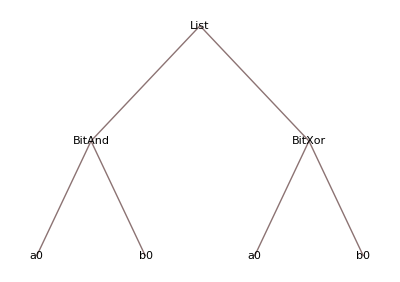

```mathematica
TreeForm[HalfAdder[a0,b0]]
```

```mathematica
HalfAdder[a0,b0]
```

{BitAnd[a0,b0],BitXor[a0,b0]}

```mathematica
PlotCompactInteractiveSystem[HalfAdder[a0,b0],ImageSize->Small]
```

### Full adder

-Graphics-

```mathematica
FullAdder[a_,b_,c_]:=Block[{halfAdd1,halfAdd2},
halfAdd1 = HalfAdder[a,b];
halfAdd2 = HalfAdder[Last[halfAdd1],c];
{BitOr[First[halfAdd1],First[halfAdd2]],Last[halfAdd2]}
];
```

#### Example

```mathematica
VisualizeAdder[FullAdder,3,"Carry"]
```

A | B | C | Carry | Result
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1

#### Visualization

```mathematica
PlotCompactInteractiveSystem[FullAdder[a0,b0,c0],ImageSize->Small]
```

### Ripple carry adder

-Graphics-

```mathematica
ALUAdder[A_,B_,carry_:0]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[B];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{carry,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{First[bigEndianSum],Rest[bigEndianSum]}];
];
```

#### Example:

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUAdder,Transpose[pairs]];
labels = {"A","B","Carry","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Carry | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 0 | {0,1}
{0,0} | {1,0} | 0 | {1,0}
{0,0} | {1,1} | 0 | {1,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {1,0}
{0,1} | {1,0} | 0 | {1,1}
{0,1} | {1,1} | 1 | {0,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {1,1}
{1,0} | {1,0} | 1 | {0,0}
{1,0} | {1,1} | 1 | {0,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 1 | {0,0}
{1,1} | {1,0} | 1 | {0,1}
{1,1} | {1,1} | 1 | {1,0}

```mathematica
PlotCompactInteractiveSystem[ALUAdder[{a1,a2,a3},{b1,b2,b3}]]
```

### Substractor

```mathematica
ALUSubstractor[A_,B_,borrow_:1]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[BitNot[B]];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{borrow,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{BitNot[First[bigEndianSum]],Rest[bigEndianSum]}];
];
```

### Opcodes

The control unit selects which operation result to get by sending an opcode to the ALU.

```mathematica
aluMnemonics = {"Add","Substract","Increment","Decrement","Pass"};
aluOpcodes = Thread[aluMnemonics->Take[Tuples[{0,1},3],Length[aluMnemonics]]];
revAluOpcodes = Map[Reverse,aluOpcodes];
ALUOpCode[mnemonic_]:=ReplaceAll[mnemonic,aluOpcodes];
```

```mathematica
Column@aluOpcodes
```

Add→{0,0,0}
Substract→{0,0,1}
Increment→{0,1,0}
Decrement→{0,1,1}
Pass→{1,0,0}

### Execution

Flags

```mathematica
ALUZero[a_]:=BitNot[Apply[BitOr,a]];
ALUNotZero[a_]:=Apply[BitOr,a];
ALUParity[a_]:=Apply[BitXor,a];
```

ALU interface

```mathematica
ALUExecute[opcode_,a_,b_]:=Block[
{
add,substract,
increment,decrement,pass,output,positiveFlag,
negativeFlag,parityFlag
},

add = ALUAdder[a,b];
substract = ALUSubstractor[a,b];
increment = ALUAdder[PadLeft[{1},Length[a]],a];
decrement = ALUSubstractor[a,PadLeft[{1},Length[a]]];
pass = a;

output = Multiplexer3BitToMBit[Length[a],opcode,
{
{ALUOpCode["Add"],Last[add]},
{ALUOpCode["Substract"],Last[substract]},
{ALUOpCode["Increment"],Last[increment]},
{ALUOpCode["Decrement"],Last[decrement]},
{ALUOpCode["Pass"],pass}
}
];

positiveFlag = Multiplexer3BitTo1Bit[opcode,
{
{ALUOpCode["Add"],1},
{ALUOpCode["Substract"],BitNot[First[substract]]},
{ALUOpCode["Increment"],1},
{ALUOpCode["Decrement"],BitNot[First[decrement]]},
{ALUOpCode["Pass"],0}
}
];

negativeFlag = Multiplexer3BitTo1Bit[opcode,
{
{ALUOpCode["Add"],0},
{ALUOpCode["Substract"],First[substract]},
{ALUOpCode["Increment"],0},
{ALUOpCode["Decrement"],First[decrement]},
{ALUOpCode["Pass"],0}
}
];

Return[<|"Positive"->positiveFlag,"Negative"->negativeFlag,"Zero"->ALUZero[output],"NotZero"->ALUNotZero[output],"Parity"->ALUParity[output],"Result"->output|>];
];
ALUExecute[opcode_,a_]:=ALUExecute[opcode,a,ConstantArray[0,Length[a]]];
```

#### Example:

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Add"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

18

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Substract"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

4

```mathematica
ALUExecute[ALUOpCode["Pass"],DecimalToBinary[11],DecimalToBinary[7]]
```

<|Positive→0,Negative→0,Zero→0,NotZero→1,Parity→1,Result→{0,0,0,0,1,0,1,1}|>

#### Visualization

```mathematica
PlotCompactInteractiveSystem[
Values[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6,
"ShowLabels"->None
]
```

## Opcodes

OpCode[mnemonic] returns the opcode associated with mnemonic.

```mathematica
cpuMnemonics = {
"LoadA","LoadB","SetA","SetB","Store","Add",
"Substract","Increment","Decrement","Jump","JumpPos","JumpNeg","JumpZero","JumpNotZero","JumpOdd",
"Call","Return","Print","Halt"
};
opcodes = Thread[cpuMnemonics->Take[Tuples[{0,1},8],Length[cpuMnemonics]]];
revOpcodes = Map[Reverse,opcodes];
OpCode[mnemonic_]:=ReplaceAll[mnemonic,opcodes];
```

```mathematica
Column[opcodes]
```

LoadA→{0,0,0,0,0,0,0,0}
LoadB→{0,0,0,0,0,0,0,1}
SetA→{0,0,0,0,0,0,1,0}
SetB→{0,0,0,0,0,0,1,1}
Store→{0,0,0,0,0,1,0,0}
Add→{0,0,0,0,0,1,0,1}
Substract→{0,0,0,0,0,1,1,0}
Increment→{0,0,0,0,0,1,1,1}
Decrement→{0,0,0,0,1,0,0,0}
Jump→{0,0,0,0,1,0,0,1}
JumpPos→{0,0,0,0,1,0,1,0}
JumpNeg→{0,0,0,0,1,0,1,1}
JumpZero→{0,0,0,0,1,1,0,0}
JumpNotZero→{0,0,0,0,1,1,0,1}
JumpOdd→{0,0,0,0,1,1,1,0}
Call→{0,0,0,0,1,1,1,1}
Return→{0,0,0,1,0,0,0,0}
Print→{0,0,0,1,0,0,0,1}
Halt→{0,0,0,1,0,0,1,0}

## CPU

This CPU contains two general purpose registers A and B which can hold 8 bit values, an addressRegister which points to the current execution address, a instructionRegister and a parameterRegister also of length 8 bit and a stackPointerRegister that cannot exceed in value the maximum stack depth of 8.

The arithmetic and logical unit has the following flags
ALUPositiveFlag
ALUNegativeFlag
ALUZeroFlag
ALUNotZeroFlag
ALUParityFlag
that can be used as arguments of JumpConditional.

UpdateParity[] update the parity flag. 
UpdateALU[numericResult] updates the flags ALUPositiveFlag, ALUNegativeFlag, ALUZeroFlag, and ALUNotZeroFlag according to the base 10 number numericResult.
LoadA[address] loads the content of RAM at address to the A register.
LoadB[address] loads the content of RAM at address to the B register.
SetA[value] set register A with value.
SetB[value] set register B with value.
Store[address] store the value of register A to the memory location address.
Add[] add the value of register A to the value of register B and store it in register A.
Substract[]  substract the value of register A to the value of register B and store it in register A.
UIncrement[] increment in one unit the value of register A.
UDecrement[] decrement in one unit the value of register A.
Jump[address] set addressRegister to the value of address.
JumpConditional[address, condition] set addressRegister to the value of address if the register at condition has value of 1.
Call[address] store current addressRegister value on the stack and  jump to address.
ReturnC[] set addressRegister to the last value of the stack. If the stack is empty, halt the machine.
PrintA[address] print the value of RAM at address in the output buffer.
ResetCPU[] reset registers, flags and RAM to zero.
AddressAdvance[] increase addressRegister by one unit.
CPU[] perform one CPU cycle.

```mathematica
DecimalToBinary[n_,size_ :8]:=PadLeft[IntegerDigits[n,2],size];
BinaryNot[0]=1;
BinaryNot[1]=0;
BinaryToDecimal[l_]:=FromDigits[l,2];
BinaryIncrement[l_,n_ :1]:=DecimalToBinary[BinaryToDecimal[l]+n,Length[l]];
BinaryDecrement[l_, n_ :1]:=DecimalToBinary[BinaryToDecimal[l]-n,Length[l]];

ExecuteALU[opcode_ : ALUOpCode["Pass"]]:=Block[{aluResult},
aluResult = ALUExecute[opcode,ARegister,BRegister];
ALUPositiveFlag = aluResult["Positive"];
ALUNegativeFlag= aluResult["Negative"];
ALUZeroFlag= aluResult["Zero"];
ALUNotZeroFlag= aluResult["NotZero"];
ALUParityFlag = aluResult["Parity"];
Return[aluResult["Result"]];
];
LoadA[address_]:=Block[{},
ARegister = RAM[[BinaryToDecimal[address]+1]];
ExecuteALU[];
AddressAdvance[];
];
LoadB[address_]:=Block[{},
BRegister = RAM[[BinaryToDecimal[address]+1]];
AddressAdvance[];
];
SetA[value_]:=Block[{},
ARegister = value;
ExecuteALU[];
AddressAdvance[];
];
SetB[value_]:=Block[{},
BRegister = value;
AddressAdvance[];
];
Store[address_]:=Block[{},
RAM[[BinaryToDecimal[address]+1]] = ARegister;
AddressAdvance[];
];
Add[]:=Block[{numericResult},
ARegister = ExecuteALU[ALUOpCode["Add"]];
AddressAdvance[];
];
Substract[]:=Block[{numericResult},
ARegister = ExecuteALU[ALUOpCode["Substract"]];
AddressAdvance[];
];
UIncrement[]:=Block[{numericResult},
ARegister = ExecuteALU[ALUOpCode["Increment"]];
AddressAdvance[];
];
UDecrement[]:=Block[{numericResult},
ARegister = ExecuteALU[ALUOpCode["Decrement"]];
AddressAdvance[];
];
Jump[address_]:=(addressRegister = address);
JumpConditional[address_,condition_]:=If[condition==1,
addressRegister = address;
,
AddressAdvance[];
];

Call[address_]:=Block[{stackAddress},
stackAddress = BinaryToDecimal[stackPointerRegister]+1;
stack[[stackAddress]]= addressRegister;
stackPointerRegister = BinaryIncrement[stackPointerRegister];
addressRegister = address;
];
ReturnC[]:=Block[{stackAddress},
If[BinaryToDecimal[stackPointerRegister]≠0,
stackPointerRegister = BinaryDecrement[stackPointerRegister];
stackAddress = BinaryToDecimal[stackPointerRegister]+1;
addressRegister = stack[[stackAddress]];
stack[[stackAddress]] = {0,0,0,0,0,0,0,0};
AddressAdvance[];
,
halted = True;
];
];
PrintA[address_]:=Block[{},
AppendTo[outputBuffer,BinaryToDecimal[Part[RAM,BinaryToDecimal[address]+1]]];
AddressAdvance[];
];

ResetCPU[]:=Block[{},
halted = False;
ARegister = {0,0,0,0,0,0,0,0};
BRegister = {0,0,0,0,0,0,0,0};

addressRegister = {0,0,0,0,0,0,0,0};
instructionRegister = {0,0,0,0,0,0,0,0};
parameterRegister = {0,0,0,0,0,0,0,0};
stackPointerRegister = {0,0,0,0,0,0,0,0};

ALUPositiveFlag = 0;
ALUNegativeFlag = 0;
ALUZeroFlag = 0;
ALUNotZeroFlag = 0;
ALUParityFlag = 0;

RAM = ConstantArray[{0,0,0,0,0,0,0,0},256];
stack = ConstantArray[{0,0,0,0,0,0,0,0},8];

outputBuffer = {};
];
ResetCPU[];

AddressAdvance[]:=(addressRegister = BinaryIncrement[addressRegister,2]);
CPU[]:=Block[{},
If[!halted,
instructionRegister = Part[RAM,BinaryToDecimal[addressRegister]+1];
parameterRegister = Part[RAM,BinaryToDecimal[addressRegister]+2];

If[instructionRegister == OpCode["LoadA"], LoadA[parameterRegister]];
If[instructionRegister == OpCode["LoadB"],LoadB[parameterRegister]];
If[instructionRegister == OpCode["SetA"], SetA[parameterRegister]];
If[instructionRegister == OpCode["SetB"], SetB[parameterRegister]];
If[instructionRegister == OpCode["Store"], Store[parameterRegister]];
If[instructionRegister == OpCode["Add"], Add[]];
If[instructionRegister == OpCode["Substract"], Substract[]];
If[instructionRegister == OpCode["Increment"], UIncrement[]];
If[instructionRegister == OpCode["Decrement"], UDecrement[]];
If[instructionRegister == OpCode["Print"],PrintA[parameterRegister]];

If[instructionRegister == OpCode["Jump"], Jump[parameterRegister]];
If[instructionRegister == OpCode["JumpPos"], JumpConditional[parameterRegister,ALUPositiveFlag]];
If[instructionRegister == OpCode["JumpNeg"], JumpConditional[parameterRegister,ALUNegativeFlag]];
If[instructionRegister == OpCode["JumpZero"], JumpConditional[parameterRegister,ALUZeroFlag]];
If[instructionRegister == OpCode["JumpNotZero"], JumpConditional[parameterRegister,ALUNotZeroFlag]];
If[instructionRegister == OpCode["JumpOdd"], JumpConditional[parameterRegister,BinaryNot[ALUParityFlag]]];
If[instructionRegister == OpCode["Call"],Call[parameterRegister]];
If[instructionRegister == OpCode["Return"],ReturnC[]];
]
];
```

## Plotting

RAMPlot[] plot the content of RAM.
ALUStatusPlot[] plot the ALU registers.
CUStatusPlot[] plot the CU registers.
StackPlot[] plot the content of the stack.
CPUPlot[] plot RAM, ALU, CU and stack.

```mathematica
HalfSplit[l_]:=Block[{len},
len = Length[l]/2;
{Take[l,len],Drop[l,len]}
];
BinaryToHex[n_]:=BaseForm[FromDigits[n,2],16];

RAMPanel[RAM_,base_]:=Block[{currentAddress,cursor,ramInDecimal},
currentAddress = BinaryToDecimal[addressRegister];
cursor = currentAddress-base+2;
If[Negative[cursor], cursor = 0];

ramInDecimal = Map[BinaryToDecimal,RAM];
Grid[Join[{{"Address","Binary value","Decimal value"}},Thread[{Range[base,base+15],RAM,ramInDecimal}]],Background->{None,{1->LightGreen,cursor->Yellow}},Frame->All]
];
RAMPlot[]:=Block[{tabs,currentTab},
tabs = MapThread[RAMPanel,{Partition[RAM,16],Range[0,255,16]}];
currentTab = Ceiling[(BinaryToDecimal[addressRegister]+1)/16];

Panel[TabView[Thread[Range[0,255,16]->tabs],currentTab],Style["RAM",Bold]]
];

ALUStatusPlot[]:=Panel[
Grid[{
{"Positive: ",ALUPositiveFlag},
{"Negative: ",ALUNegativeFlag},
{"Zero: ",ALUZeroFlag},
{"NotZero: ",ALUNotZeroFlag},
{"Parity: ",ALUParityFlag}
},
Frame->All,
Background->{{LightRed},None}
],
Style["ALU Status",Bold]
];

$OldALUOpcode = None;
$OldRegisterA = None;
$OldRegisterB = None;
$OldALUPlot = None;
ALUPlot[]:=Block[{aluOpcode,aluPlot},
aluOpcode = Switch[instructionRegister,
OpCode["Add"],ALUOpCode["Add"],
OpCode["Substract"],ALUOpCode["Substract"],
OpCode["Increment"],ALUOpCode["Increment"],
OpCode["Decrement"],ALUOpCode["Decrement"],
_,ALUOpCode["Pass"]
];

If[aluOpcode===$OldALUOpcode && ARegister===$OldRegisterA && BRegister===$OldRegisterB,
aluPlot = $OldALUPlot,

$OldALUOpcode = aluOpcode;
$OldRegisterA = ARegister;
$OldRegisterB = BRegister;

(*{a1,a2,a3,a4,a5,a6,a7,a8},{b1,b2,b3,b4,b5,b6,b7,b8}*)
aluPlot= CompactEvaluatedTreeForm[
Values@ALUExecute[{o1,o2,o3},{a1,a2,a3,a4},{b1,b2,b3,b4}],
Join[
Thread[{o1,o2,o3}->aluOpcode],
Thread[{a1,a2,a3,a4,a5,a6,a7,a8}->ARegister],
Thread[{b1,b2,b3,b4,b5,b6,b7,b8}->BRegister]
],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->600,
VertexSize->0.6,
"ShowLabels"->None
];
$OldALUPlot = aluPlot;
];
Return[aluPlot];
];
CUStatusPlot[]:=Block[{mainRegisters,instructionRegisters,flagsStatus},
mainRegisters = Grid[
{
{"","Register A","Register B"},
{"Binary",Row[ARegister],Row[BRegister]},
{"Decimal",BinaryToDecimal[ARegister],BinaryToDecimal[BRegister]}
},
Frame->All,
Background->{None,{LightGreen}}
];

instructionRegisters = Grid[
{
{"Instruction Register","Address Register"},
{
Grid[
{
{"Opcode","Parameter"},
{Row[instructionRegister],Row[parameterRegister]},
{instructionRegister/.revOpcodes,BinaryToDecimal[parameterRegister]}
},
Frame->All,Background->{None,{LightCyan}}
],
Grid[
{
{"Binary",Row[addressRegister]},
{"Decimal",BinaryToDecimal[addressRegister]}
},
Frame->All,Background->{{LightCyan},None}
]
}
},
Frame->All,
Background->{None,{LightBlue}}
];
Panel[Column[{mainRegisters,instructionRegisters}],Style["CU Status",Bold],ImageSize->300]
];
StackPlot[]:=Block[{cursor,stackInDecimal,plt},
cursor = BinaryToDecimal[stackPointerRegister]+2;
stackInDecimal = Map[BinaryToDecimal,stack];
plt = Join[{{"Stack level","Binary value","Decimal value"}},Thread[{Range[1,8],stack,stackInDecimal}]];
Panel[Grid[plt,Background->{None,{1->LightGreen,cursor->Yellow}},Frame->All],Style["Stack",Bold]]
];

CPUPlot[]:=Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[],StackPlot[]}],RAMPlot[]}},Alignment->Top],Style["CPU",Bold]];
```

## Load program to memory

LoadProgram[program] load program to RAM.
ClearProgram[] clear RAM and fill it with zero values.

```mathematica
LoadProgram[program_]:=Block[{x},RAM = PadRight[program,256,x]/.x->{0,0,0,0,0,0,0,0}];
ClearProgram[]:=(RAM = ConstantArray[{0,0,0,0,0,0,0,0},256]);
```

## Machine code generation

For the conversion of ASM code to machine code all the labels (IC arguments enclosed in <>) need to be converted to memory positions. 
CPUGetInstructions[asmcode] formats assembly code into a nested list.
CPUGetPosition[instructions, token] calculates the final position of a given token considering that Labels occupy 0 bits in the machine code, Declare 1 byte, and any other instruction 2 bytes.
CPUProcessTags[instructions] generates the substitution rule for converting labels to memory positions.
CPUMachineInstructions[instructions] returns the exact instructions that will be assembled.
CPUAssemblyCompile[asmcode] compiles ASM to machine code.

```mathematica
CPUGetInstructions[asmcode_]:=Block[{separated,completed},
separated = DeleteCases[Map[StringSplit,StringSplit[asmcode,"\n"]],{}];
completed = ReplaceAll[separated,l_/;(Length[l]==1):>Append[l,0]];
Return[completed];
];
CPUGetPosition[instructions_,token_]:=Block[{pos,labels,countingRules},
pos = Position[instructions,token];
If[Length[pos]>1,Return[$Failed]];
labels = Take[instructions,pos[[1,1]]-1][[All,1]];
countingRules = Join[Thread[cpuMnemonics->2],{"Label"->0,"Declare"->1}];

Total[ReplaceAll[labels,countingRules]]
];
CPUProcessTags[instructions_]:=Block[{labels,variablePos},
labels = Cases[instructions,{"Label",tag_}:>(tag->CPUGetPosition[instructions,{"Label",tag}])];
variablePos = Cases[instructions,{"Declare",tag_,value_}:>(tag->CPUGetPosition[instructions,{"Declare",tag,value}])];
Join[labels,variablePos]
];
CPUMachineInstructions[instructions_]:=Block[{setNumeric,removeLabels,replaceTags},
setNumeric = ReplaceAll[instructions,{{"Declare",_,value_}:>ToExpression[value],{"SetA",value_}:>{"SetA",ToExpression[value]},{"SetB",value_}:>{"SetB",ToExpression[value]} }];
removeLabels = DeleteCases[setNumeric,{"Label",__}];
replaceTags = ReplaceAll[removeLabels,CPUProcessTags[instructions]];

Return[replaceTags];
];
CPUAssemblyCompile[asmcode_]:=Block[{linearized,rules, machineCode},
linearized = Flatten[CPUMachineInstructions[CPUGetInstructions[asmcode]]];
rules = Append[opcodes,n_Integer:>DecimalToBinary[n]];
machineCode = ReplaceAll[linearized,rules];
Return[machineCode];
];
```

## Execution visualization

InstructionsPlot[code] plot the instructions in assembler.
OutputPlot[] plot the output buffer.
ExecutionPlot[code] plot RAM, ALU, CU, output, instructions and stack.
ViewExecution[code, maxIterations] view every execution step in a dynamic panel.

```mathematica
InstructionsPanel[machineInstructions_,from_]:=Block[{cursor,instructions},
cursor = BinaryToDecimal[addressRegister]-from+1;
If[Negative[cursor], cursor = 0];
instructions = Thread[{Range[from,from+Length[Flatten[machineInstructions]]-1],Flatten[machineInstructions]}];

Grid[
instructions,
Background->{{LightGreen},{cursor->Yellow}}
]
];
InstructionsPlot[code_]:=Block[{mi,tabs,currentAddress,currentTab},
mi =Flatten[CPUMachineInstructions[CPUGetInstructions[code]]];
tabs = MapThread[InstructionsPanel,{Partition[mi,UpTo[16]],Range[0,Length[mi]-1,16]}];

currentTab = Ceiling[(BinaryToDecimal[addressRegister]+1)/16];

Panel[TabView[Thread[Range[0,Length[mi]-1,16]->tabs],currentTab],Style["Program",Bold]]
];
```

```mathematica
ColumnJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""],"\n"]];
OutputPlot[]:=Panel[
InputField[
ColumnJoin[Map[ToString,outputBuffer]],String,
FieldSize->{10,{0,Infinity}},
Enabled->False
],
Style["Output",Bold]
];
ExecutionPlot[code_]:=Block[{cpuPanel,aluPanel,memoryAndOutput},
cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[],StackPlot[]}]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{InstructionsPlot[code],RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{cpuPanel,memoryAndOutput}]
];
ExecutionPlotWithALU[code_]:=Block[{cpuPanel,aluPanel,memoryAndOutput},
cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[],StackPlot[]}]}},Alignment->Top],Style["CPU",Bold]];
aluPanel = Panel[ALUPlot[],Style["ALU Graph",Bold]];
memoryAndOutput = Panel[Grid[{{InstructionsPlot[code],RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{Row[{cpuPanel,aluPanel}],memoryAndOutput}]
];

Options[ViewExecution]={"ShowALU"->False};
ViewExecution[code_,maxIterations_,OptionsPattern[]]:=DynamicModule[{program,frames, i = 0},
ResetCPU[];
program = CPUAssemblyCompile[code];
LoadProgram[program];
frames = {If[OptionValue["ShowALU"],ExecutionPlotWithALU[code],ExecutionPlot[code]]};

While[!halted && i<maxIterations,
CPU[];
AppendTo[frames,If[OptionValue["ShowALU"],ExecutionPlotWithALU[code],ExecutionPlot[code]]];
i++;
];

Manipulate[frames[[iteration]],{iteration,1,Length[frames],1}]
];
```

# Program execution

## Assembled code

```mathematica
code = "
LoadA <main::n1>
Store <divide::n1>
LoadA <main::n2>
Store <divide::n2>
Call <divide>
Store <main::result>
Print <main::result>
Halt
Declare <main::n1> 20
Declare <main::n2> 5
Declare <main::result> 0
Label <divide>
LoadA <divide::zero>
Store <divide::result>
Label <divide::begin_loop>
LoadA <divide::result>
Increment
Store <divide::result>
LoadA <divide::n1>
LoadB <divide::n2>
Substract
Store <divide::n1>
JumpNeg <divide::end_loop>
Jump <divide::begin_loop>
Label <divide::end_loop>
LoadA <divide::result>
Decrement
Return
Declare <divide::n1> 0
Declare <divide::n2> 0
Declare <divide::result> 0
Declare <divide::zero> 0
";
```

```mathematica
ViewExecution[code,15,"ShowALU"->True]
```

## Compiled code

```mathematica
Needs["PL0Compiler`",FileNameJoin[{NotebookDirectory[],"Packages","Compiler.wl"}]];
?PL0Compiler`*
```

```mathematica
asm = CompilePL0ToASM["var x,y,z;
begin
   x := 0;
   y := 1;
   z := 1;

   while z < 50 do
   begin
      z := x + y;
      print z;
      x := y;
      y := z;
   end;
end."];
```

```mathematica
asm
```

SetA 0
Store <x>
SetA 1
Store <y>
SetA 1
Store <z>
Label <0::L1>
SetA 50
LoadB <z>
Substract
JumpNeg <0::L2>
LoadA <x>
LoadB <y>
Add
Store <$0>
LoadA <$0>
Store <z>
Print <z>
LoadA <y>
Store <x>
LoadA <z>
Store <y>
Jump <0::L1>
Label <0::L2>
Return
Declare <x> 0
Declare <y> 0
Declare <$0> 0
Declare <z> 0

```mathematica
MachineInstructions[GetInstructions[asm]]
```

{{SetA,0},{Store,46},{SetA,1},{Store,47},{SetA,1},{Store,49},{SetA,50},{LoadB,49},{Substract,0},{JumpNeg,44},{LoadA,46},{LoadB,47},{Add,0},{Store,48},{LoadA,48},{Store,49},{Print,49},{LoadA,47},{Store,46},{LoadA,49},{Store,47},{Jump,12},{Return,0},0,0,0,0}

```mathematica
ViewExecution[asm,300]
```